# 2. Norms

## Norms

A norm ||.|| is just a way to measure how big something (a vector or a matrix in our course) is.  Any norm needs to satisfy the following
	1) ||x||≥0  and ||x||=0 implies x is zero.
	2) ||x+y||≤||x||+||y||
	3) ||α x||=|α| ||x||

## Vector Norms: ||x(||)_p

Useful vector norms are ||x(||)_p^p=∑_(i=1)^m |x_i|^p with p≥1. This includes the familiar Euclidean norm p=2, and in the lmit as p→∞ the pessimists norm||x(||)_∞=max_i |x_i|. All are available in most software package.  I would hope the default is always the 2 norm!

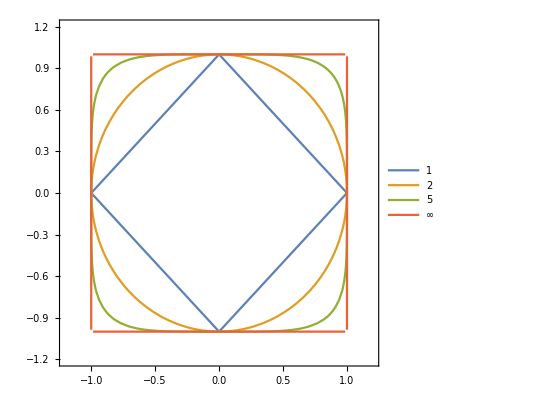

```mathematica
p=5;
ContourPlot[ {
Norm[{x1,x2},1]==1,Norm[{x1,x2},2]==1,Norm[{x1,x2},p]==1,Norm[{x1,x2},∞]==1},{x1,-1.2,1.2},{x2,-1.2,1.2},
PlotLegends->{1,2,p,∞}]
```

## Matrix Norms: ||A||

There are lots of useful norms for A∈ℂ^(m×n)! Different packages have different defaults! You should always check what you are computing!

### Frobenius Norm: ||A(||)_F

One useful norm is the Hilbert-Schmidt or Frobenius norm 
	||A(||)_F^2=∑_(i=1)^m ∑_(j=1)^n|A_(i,j)|^2=∑_(j=1)^n ||a_j(||)_2^2

### Induced Vector Norms: ||A(||)_p

Each vector p-norm defines (fancy word induces) a norm for matrices A∈ℂ^(m×n) via 
	||A(||)_(m,n)=max_(x≠0) (||A.x(||)_(m))/(||x(||)_(n))=max_(||x(||)_(n)=1) ||A.x(||)_(m)
The matrix norm induced by the two norm is the most common of these. It is the default in Mathematica.

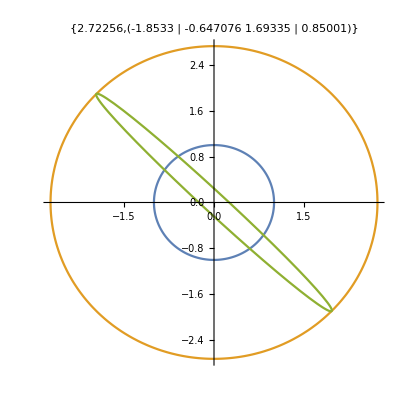

```mathematica
A=RandomReal[{-2,2},{2,2}];
s=Norm[A];
ParametricPlot[{{Cos[θ],Sin[θ]},s{Cos[θ],Sin[θ]},A.{Cos[θ],Sin[θ]}},{θ,0,2π},PlotRange->All,
PlotLabel->{s,A}]
```